```mathematica
etaNC = DRhoOverT*Log[rho] -rho;
```

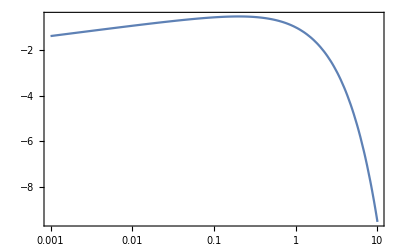

```mathematica
etaOfRhoPlt = LogLinearPlot[etaNC/.{DRhoOverT->.2},{rho,0.001,10}, PlotRange->All, Frame->{True, True, False,False}]
```

```mathematica
Export[NotebookDirectory[]<>"etaNCOfRhoMinimalModel.pdf", etaOfRhoPlt]
```